```mathematica
<<SymbolicComputing`
<<Notation`
Symbolize[ParsedBoxWrapper[SubscriptBox["_","_"]]]                                (* To use variables with subscripts! *)
DateString[]
$Version
$SCVersion
```

Wed 5 Apr 2023 15:29:01

13.2.0 for Microsoft Windows (64-bit) (November 18, 2022)

6.0.2 (June 28, 2021)

## Lecture 10 edited by Chi-Ok Hwang, originally made by Dr. 전 경원

[1] C. Arangala and K. A. Yokley, Exploring Calculus: Labs and Projects with Mathematica, 1st ed. Chapman and Hall/CRC, 2016.

-Graphics-

MathSymbolica Package

Winners of Wolfram Innovator Award 2017

-Graphics-

## Fourier series

```mathematica
ComplexExpand[FourierSeries[t/2,t,5]]       (* Find the 5^(th)-order Fourier series of t/2  *)
```

Sin[t]-1/2 Sin[2 t]+1/3 Sin[3 t]-1/4 Sin[4 t]+1/5 Sin[5 t]

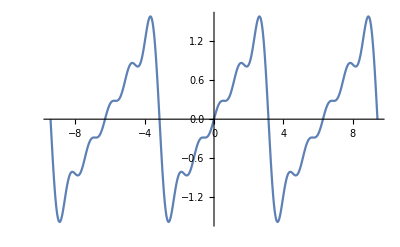

```mathematica
Plot[%,{t,-3Pi,3Pi}]
```

## TrigExpand

```mathematica
TrigExpand[Sin[2 x]]
```

2 Cos[x] Sin[x]

```mathematica
TrigExpand[Sin[x+y]]
```

Cos[y] Sin[x]+Cos[x] Sin[y]

```mathematica
TrigReduce[2 Sin[x]^2]
```

1-Cos[2 x]

```mathematica
TrigReduce[2 Sin[x]^2];
TrigExpand[%]
```

1-Cos[x]^2+Sin[x]^2

```mathematica
TrigReduce[2 Sin[x]^2];
TrigExpand[%];
%-2 Sin[x]^2
```

1-Cos[x]^2-Sin[x]^2

```mathematica
TrigExpand[Sin[x]^2+Tan[x]^2]
```

-1/2-Cos[x]^2/8+(5 Sec[x]^2)/8+(3 Sin[x]^2)/4+Tan[x]^2/2-1/8 Sin[x]^2 Tan[x]^2

```mathematica
TrigFactor[Sin[x]^2+Tan[x]^2]
```

1/2 (3+Cos[2 x]) Tan[x]^2

```mathematica
TrigFactor[Sin[x]^2+Tan[x]^2]
```

1/2 (3+Cos[2 x]) Tan[x]^2

## Complex numbers

```mathematica
Sqrt[-4]
```

2 ⅈ

```mathematica
(4+3 I)/(2-I)
```

1+2 ⅈ

```mathematica
Exp[2+9 I]//N
```

-6.73239+3.04517 ⅈ

```mathematica
ComplexExpand[Tan[x+I y]]
```

Sin[2 x]/(Cos[2 x]+Cosh[2 y])+(ⅈ Sinh[2 y])/(Cos[2 x]+Cosh[2 y])

```mathematica
ReIm[{I,-1,-I,1}]
```

{{0,1},{-1,0},{0,-1},{1,0}}

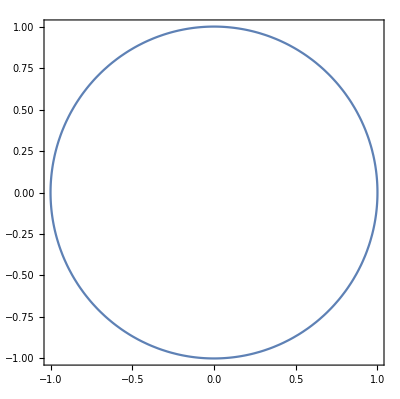

```mathematica
ClearAll["Global`*"]
ParametricPlot[{Re[ⅇ^(ⅈ x)],Im[ⅇ^(ⅈ x)]},{x,0,2Pi}, Frame -> True]
```

```mathematica
ClearAll["Global`*"]
 z=ⅇ^(ⅈ x)
ParametricPlot[{Re[z],Im[z]},{x,0,2Pi}, Frame -> True]
```

ⅇ^(ⅈ x)

-Graphics-

```mathematica
ClearAll["Global`*"]
 z[x_]:=ⅇ^(ⅈ x)
ParametricPlot[{Re[z[x]],Im[z[x]]},{x,0,2Pi}, Frame -> True]
```

-Graphics-

```mathematica
ClearAll["Global`*"]
z == ⅇ^(ⅈ x)
ParametricPlot[ReIm[z],{x,0,2Pi}, Frame -> True]
```

z==ⅇ^(ⅈ x)

-Graphics-

```mathematica
ClearAll["Global`*"]
 z[x_]:=ⅇ^(ⅈ x)
ParametricPlot[{Re[z],Im[z]},{x,0,2Pi}, Frame -> True]
```

-Graphics-

```mathematica
ClearAll["Global`*"]
z = ⅇ^(ⅈ x)
x = 3
z
ReIm[z]
```

ⅇ^(ⅈ x)

3

ⅇ^(3 ⅈ)

{Cos[3],Sin[3]}

## The Squeeze Theorem

The squeeze theorem states that if f(x)≤g(x)≤h(x) when x is near a (except possibly at a) and lim_(x→a) f(x)=lim_(x→a) h(x)=L then lim_(x→a) g(x)=L.

Demonstration: Squeeze Theorem

```mathematica
Manipulate[Plot[{-Abs[x]^n,x^n Sin[1/x],Abs[x]^n},{x,-.1,.1},
PlotLegends->"Expressions"],{n,{1,2,3}}]
```

Determine lim_(x→0) x sin(1/x).

```mathematica
Simplify[Abs[x]-x Sin[1/x]≥0,Assumptions->{x≠0&&x∈Reals}]
```

True

```mathematica
Simplify[x Sin[1/x]-(-Abs[x])≥0,Assumptions->{x≠0&&x∈Reals}]
```

True

```mathematica
Limit[{Abs[x],-Abs[x]},x->0]
```

{0,0}

Therefore, lim_(x→0) x sin(1/x)=0 by the squeeze theorem.

Determine lim_(x→0) x^2 sin(1/x).

```mathematica
Simplify[Abs[x]^2-x^2 Sin[1/x]≥0,Assumptions->{x≠0&&x∈Reals}]
```

True

```mathematica
Simplify[x^2 Sin[1/x]-(-Abs[x]^2)≥0,Assumptions->{x≠0&&x∈Reals}]
```

True

```mathematica
Limit[{Abs[x]^2,-Abs[x]^2},x->0]
```

{0,0}

Therefore, lim_(x→0) x^2 sin(1/x)=0 by the squeeze theorem.

Determine lim_(x→0) x^3 sin(1/x).

```mathematica
Simplify[Abs[x]^3-x^3 Sin[1/x]≥0,Assumptions->{x≠0&&x∈Reals}]
```

True

```mathematica
Simplify[x^3 Sin[1/x]-(-Abs[x]^3)≥0,Assumptions->{x≠0&&x∈Reals}]
```

True

```mathematica
Limit[{Abs[x]^3,-Abs[x]^3},x->0]
```

{0,0}

Therefore, lim_(x→0) x^3 sin(1/x)=0 by the squeeze theorem.

Determine lim_(x→∞) (sin(x))/x.

```mathematica
Simplify[Abs[1/x]-Sin[x]/x≥0,Assumptions->{x≠0&&x∈Reals}]
```

True

```mathematica
Simplify[Sin[x]/x-(-Abs[1/x])≥0,Assumptions->{x≠0&&x∈Reals}]
```

True

```mathematica
Limit[{Abs[1/x],-Abs[1/x]},x->∞]
```

{0,0}

Therefore, lim_(x→∞) (sin(x))/x=0 by the squeeze theorem.

Determine lim_(x→∞) (cos(2x))^2/(2x-3).

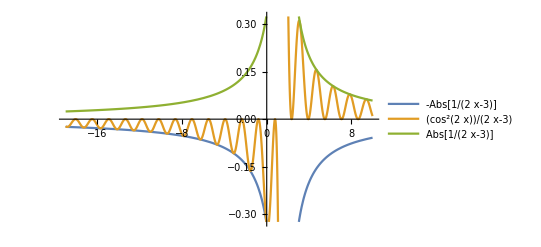

```mathematica
Plot[{-Abs[1/(2x-3)],Cos[2x]^2/(2x-3),Abs[1/(2x-3)]},{x,-19,10},PlotLegends->"Expressions"]
```

```mathematica
Simplify[Abs[1/(2x-3)]-Cos[2x]^2/(2x-3)≥0,Assumptions->{x≠3/2&&x∈Reals}]
```

True

```mathematica
Simplify[Cos[2x]^2/(2x-3)-(-Abs[1/(2x-3)])≥0,Assumptions->{x≠3/2&&x∈Reals}]
```

True

```mathematica
Limit[{Abs[1/(2x-3)],-Abs[1/(2x-3)]},x->∞]
```

{0,0}

Therefore, lim_(x→∞) (cos(2x))^2/(2x-3)=0 by the squeeze theorem.

## Applying the Intermediate Value Theorem

The Intermediate Value Theorem states that if a function f(x) is continuous on the closed interval [a,b] and f(a)<c<f(b) then ∃x∈ [a,b] s.t. f(x)=c.

Exercises:

Estimate the root of a function, f(x)=7 x^3-22 x^2-35x+110, using the Bisection Method with the Intermediate Value Theorem.

a, b. Plot f(x) and determine the number of root.s

f[x]==110-35 x-22 x^2+7 x^3

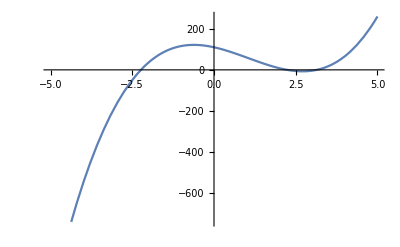
f[x]==-Graphics-

```mathematica
f[x]==7 x^3-22 x^2-35x+110
SCMAF[%,Plot,{At[2],{x,-5,5}}]
```

```mathematica
f[x]==7 x^3-22 x^2-35x+110
SCMAF[%,Plot,{At[2],{x,-5,5}},Take->{2}]
```

f[x]==110-35 x-22 x^2+7 x^3

-Graphics-

c. Determine f[3] and f[4].

```mathematica
{f[3],f[4]}/.f[x_]->7 x^3-22 x^2-35x+110
```

{-4,66}

```mathematica
SCARA[{f[3],f[4]},f[x_]==7 x^3-22 x^2-35x+110]
SCMAF[%,Thread,All]
```

{f[3],f[4]}=={-4,66}

{f[3]==-4,f[4]==66}

d. Show that the root exists in [3,4] using the Intermediate Value Theorem.

e. Calculate f[3.5] and determine whether the root lies in [3,3.5] or [3.5,4].

```mathematica
f[x]==7 x^3-22 x^2-35x+110/.x->3.5
```

f[3.5]==18.125

f. Generalize this procedure and find the root using FixedPoint.

If we use infinite precision numbers, we can not reach the fixed point.
(*   FixedPoint[f,expr]   starts with expr, then applies f repeatedly until the result no longer changes. *)

```mathematica
f[x_]:=7 x^3-22 x^2-35x+110
FixedPoint[If[f[#[[1]]]f[#[[2]]]<0, {#[[1]],(#[[1]]+#[[2]])/2,#[[2]]},{#[[2]],(#[[2]]+#[[3]])/2,#[[3]]}]&,{3,3.5,4}]
f[x_]=.
```

{3.14286,3.14286,3.14286}

Just two-list is enough.

```mathematica
f[x_]:=7 x^3-22 x^2-35x+110
FixedPointList[If[f[#[[1]]]f[(#[[1]]+#[[2]])/2.]<0, {#[[1]],(#[[1]]+#[[2]])/2.},{(#[[1]]+#[[2]])/2.,#[[2]]}]&,{3,4}]
f[x_]=.
```

{{3,4},{3,3.5},{3,3.25},{3.125,3.25},{3.125,3.1875},{3.125,3.15625},{3.14063,3.15625},{3.14063,3.14844},{3.14063,3.14453},{3.14258,3.14453},{3.14258,3.14355},{3.14258,3.14307},{3.14282,3.14307},{3.14282,3.14294},{3.14282,3.14288},{3.14285,3.14288},{3.14285,3.14287},{3.14285,3.14286},{3.14286,3.14286},{3.14286,3.14286},{3.14286,3.14286},{3.14286,3.14286},{3.14286,3.14286},{3.14286,3.14286},{3.14286,3.14286},{3.14286,3.14286},{3.14286,3.14286},{3.14286,3.14286},{3.14286,3.14286},{3.14286,3.14286},{3.14286,3.14286},{3.14286,3.14286},{3.14286,3.14286},{3.14286,3.14286},{3.14286,3.14286},{3.14286,3.14286},{3.14286,3.14286},{3.14286,3.14286},{3.14286,3.14286},{3.14286,3.14286},{3.14286,3.14286},{3.14286,3.14286},{3.14286,3.14286},{3.14286,3.14286},{3.14286,3.14286},{3.14286,3.14286},{3.14286,3.14286},{3.14286,3.14286},{3.14286,3.14286},{3.14286,3.14286},{3.14286,3.14286},{3.14286,3.14286}}

Verify your solution using Solve.

```mathematica
Solve[7 x^3-22 x^2-35x+110==0&&3<x<4,x]//N
```

{{x→3.14286}}

```mathematica
f[x]==7 x^3-22 x^2-35x+110
SCMAF[%,RA,{At[1],f[x]==0},
And,{All,3<x<4},
SCNSolve,{All,x}]
```

f[x]==110-35 x-22 x^2+7 x^3

0==110-35 x-22 x^2+7 x^3&&3<x<4

x==3.14286